## Funkcje tworzące i transformaty

### Funkcje tworzące

W Mathematice funkcję tworzącą ciągu {a_n} wyznaczamy w następujący sposób:

```mathematica
GeneratingFunction[a[n],n,z];
```

```mathematica
P[z_]=GeneratingFunction[PDF[PoissonDistribution[λ],n],n,z]
```

Set::write: Tag PoissonProcess in PoissonProcess[8][z_] is Protected.

ⅇ^((-1+z) λ)

Postać szeregu możemy zobaczyć używając funkcji Series

```mathematica
Series[P[z],{z,0,10}]
```

PoissonDistribution[0]+8 PoissonDistribution'[0] z+32 PoissonDistribution''[0] z^2+256/3 PoissonDistribution^(3)[0] z^3+512/3 PoissonDistribution^(4)[0] z^4+4096/15 PoissonDistribution^(5)[0] z^5+16384/45 PoissonDistribution^(6)[0] z^6+131072/315 PoissonDistribution^(7)[0] z^7+131072/315 PoissonDistribution^(8)[0] z^8+(1048576 PoissonDistribution^(9)[0] z^9)/2835+(4194304 PoissonDistribution^(10)[0] z^10)/14175+O[z]^11

Współczynnik przy wybranym składniku znajdziemy przy pomocy funkcji SeriesCoefficient

```mathematica
Table[SeriesCoefficient[P[z],{z,0,k}],{k,0,10}]
```

{PoissonDistribution[0],8 PoissonDistribution'[0],32 PoissonDistribution''[0],256/3 PoissonDistribution^(3)[0],512/3 PoissonDistribution^(4)[0],4096/15 PoissonDistribution^(5)[0],16384/45 PoissonDistribution^(6)[0],131072/315 PoissonDistribution^(7)[0],131072/315 PoissonDistribution^(8)[0],(1048576 PoissonDistribution^(9)[0])/2835,(4194304 PoissonDistribution^(10)[0])/14175}

Dla λ=1, prawdopodobieństwo, że zmienna losowa o rozkładzie Poissona przyjmie wartość 3 wynosi

```mathematica
SeriesCoefficient[P[z],{z,0,3}]/.λ->1.
```

256/3 PoissonDistribution^(3)[0]

Wartość oczekiwaną dla danego rozkładu możemy znaleźć licząc pochodną funkcji tworzącej w punkcie 1

```mathematica
D[P[z],z]/.z->1
```

8 PoissonDistribution'[8]

### Transformata Laplace’a

Transformatę Laplace’a Stieltjesa dystrybuanty rozkładu ciągłego dostaniemy wyznaczając transformatę Laplace’a jej gęstości

```mathematica
F[s_]=LaplaceTransform[PDF[ExponentialDistribution[μ],t],t,s]
```

{{(15 ⅇ^(2 y) μ)/(4 y^5+15 ⅇ^(2 y) μ),(14175 ⅇ^(2 y) μ)/(4 y^10+14175 ⅇ^(2 y) μ),(638512875 ⅇ^(2 y) μ)/(16 y^15+638512875 ⅇ^(2 y) μ),(9280784638125 ⅇ^(2 y) μ)/(4 y^20+9280784638125 ⅇ^(2 y) μ)},{(15 ⅇ^(4 y) μ)/(128 y^5+15 ⅇ^(4 y) μ),(14175 ⅇ^(4 y) μ)/(4096 y^10+14175 ⅇ^(4 y) μ),(638512875 ⅇ^(4 y) μ)/(524288 y^15+638512875 ⅇ^(4 y) μ),(9280784638125 ⅇ^(4 y) μ)/(4194304 y^20+9280784638125 ⅇ^(4 y) μ)},{(5 ⅇ^(6 y) μ)/(324 y^5+5 ⅇ^(6 y) μ),(175 ⅇ^(6 y) μ)/(2916 y^10+175 ⅇ^(6 y) μ),(875875 ⅇ^(6 y) μ)/(314928 y^15+875875 ⅇ^(6 y) μ),(1414538125 ⅇ^(6 y) μ)/(2125764 y^20+1414538125 ⅇ^(6 y) μ)},{(15 ⅇ^(8 y) μ)/(4096 y^5+15 ⅇ^(8 y) μ),(14175 ⅇ^(8 y) μ)/(4194304 y^10+14175 ⅇ^(8 y) μ),(638512875 ⅇ^(8 y) μ)/(17179869184 y^15+638512875 ⅇ^(8 y) μ),(9280784638125 ⅇ^(8 y) μ)/(4398046511104 y^20+9280784638125 ⅇ^(8 y) μ)}}

Wartość oczekiwaną zmiennej losowej można obliczyć przy pomocy pochodnej transformaty

```mathematica
-D[F[s],s]/.s->0
```

D::dvar: Multiple derivative specifier {{4/15 ⅇ^(-2 y) y^5,(4 ⅇ^(-2 y) y^10)/14175,(16 ⅇ^(-2 y) y^15)/638512875,(4 ⅇ^(-2 y) y^20)/9280784638125},{128/15 ⅇ^(-4 y) y^5,(4096 ⅇ^(-4 y) y^10)/14175,(524288 ⅇ^(-4 y) y^15)/638512875,(4194304 ⅇ^(-4 y) y^20)/9280784638125},{324/5 ⅇ^(-6 y) y^5,2916/175 ⅇ^(-6 y) y^10,(314928 ⅇ^(-6 y) y^15)/875875,(2125764 ⅇ^(-6 y) y^20)/1414538125},{4096/15 ⅇ^(-8 y) y^5,(4194304 ⅇ^(-8 y) y^10)/14175,(17179869184 ⅇ^(-8 y) y^15)/638512875,(4398046511104 ⅇ^(-8 y) y^20)/9280784638125}} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::ivar: 0 is not a valid variable.

-∂_0 {{(15 ⅇ^(2 y) μ)/(4 y^5+15 ⅇ^(2 y) μ),(14175 ⅇ^(2 y) μ)/(4 y^10+14175 ⅇ^(2 y) μ),(638512875 ⅇ^(2 y) μ)/(16 y^15+638512875 ⅇ^(2 y) μ),(9280784638125 ⅇ^(2 y) μ)/(4 y^20+9280784638125 ⅇ^(2 y) μ)},{(15 ⅇ^(4 y) μ)/(128 y^5+15 ⅇ^(4 y) μ),(14175 ⅇ^(4 y) μ)/(4096 y^10+14175 ⅇ^(4 y) μ),(638512875 ⅇ^(4 y) μ)/(524288 y^15+638512875 ⅇ^(4 y) μ),(9280784638125 ⅇ^(4 y) μ)/(4194304 y^20+9280784638125 ⅇ^(4 y) μ)},{(5 ⅇ^(6 y) μ)/(324 y^5+5 ⅇ^(6 y) μ),(175 ⅇ^(6 y) μ)/(2916 y^10+175 ⅇ^(6 y) μ),(875875 ⅇ^(6 y) μ)/(314928 y^15+875875 ⅇ^(6 y) μ),(1414538125 ⅇ^(6 y) μ)/(2125764 y^20+1414538125 ⅇ^(6 y) μ)},{(15 ⅇ^(8 y) μ)/(4096 y^5+15 ⅇ^(8 y) μ),(14175 ⅇ^(8 y) μ)/(4194304 y^10+14175 ⅇ^(8 y) μ),(638512875 ⅇ^(8 y) μ)/(17179869184 y^15+638512875 ⅇ^(8 y) μ),(9280784638125 ⅇ^(8 y) μ)/(4398046511104 y^20+9280784638125 ⅇ^(8 y) μ)}}

## Proces Poissona

```mathematica
M=PoissonProcess[λ]
```

PoissonProcess[λ]

Przykładowo wyznaczymy prawdopodobieństwo, że przez czas t proces Poissona z intensywnością λ wygeneruje mniej niż 4 zdarzenia

```mathematica
Probability[m[t]<4,m\[Distributed]M]
```

1/6 ⅇ^(-t λ) (6+6 t λ+3 t^2 λ^2+t^3 λ^3)

```mathematica
p[k_,t_]=PDF[M[t],k]
```

Piecewise[{{(ⅇ^(-t λ) (t λ)^k)/(k!), k≥0}, {0, True}}]

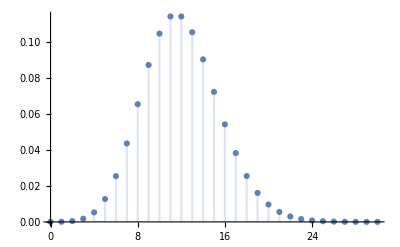

```mathematica
DiscretePlot[p[k,4]/.λ->3,{k,0,30}]
```

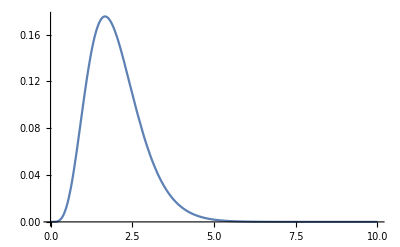

```mathematica
Plot[p[5,t]/.λ->3,{t,0,10}]
```

Generowanie procesu Poissona

```mathematica
proces=RandomFunction[M/.λ->3,{0,5}];
```

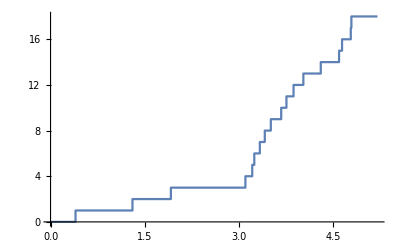

```mathematica
ListStepPlot[proces]
```

Czas pomiędzy zdarzeniami z procesu Poissona z parametrem λ ma rozkład wykładniczy z tym samym parametrem. Jeśli rozważamy dwa (ten wynik można uogólnić na większą liczbę procesów) procesy Poissona z intensywnościami λ i μ, to prawdopodobieństwo, że jako pierwsze nastąpiło zdarzenie np. z tego pierwszego procesu wynosi

```mathematica
Probability[X==Min[X,Y],{X\[Distributed]ExponentialDistribution[λ], Y\[Distributed]ExponentialDistribution[μ]}]
```

λ/(λ+μ)

### Zadania

1. Trzy razy dziennie kierowca parkuje swój samochód na pół godziny bez uiszczenia opłaty za
postój.Kontroler odwiedza każde miejsce postojowe zgodnie z procesem Poissona z parametrem λ (na godzinę).Jeśli natrafi na samochód, za który nie została wniesiona opłata, wystawia mandat.
(a) Jakie jest prawdopodobieństwo, że danego dnia kierowcy się upiecze?
(b) Jakie jest prawdopodobieństwo, że kierowca otrzyma w jednym dniu dwa mandaty?
(c) Załóżmy, że opłata za parkowanie wynosi 5 zł/h, a jednorazowa kara za nieopłacenie
miejsca wynosi 50 zł.Jaka jest wartość oczekiwana łącznej kary dla naszego niesfornego kierowcy?Jaka musiałaby być intensywność kontroli, żeby kierowcy opłacało się
ryzykować?

1. Ze względu na właściwości procesu Poissona, nie jest ważne, w jakich kawałkach kierowca parkuje samochód, istotny jest tylko łączny czas parkowania w ciągu dnia.

```mathematica
Kontrola = PoissonProcess[λ];
```

a) Szukane prawdopodobieństwo:

```mathematica
Probability[k[1.5]==0,k\[Distributed]Kontrola]
```

ⅇ^(-1.5 λ)

b) Prawdopodobieństwo, że kierowca dostanie dwa mandaty wynosi:

```mathematica
Probability[m[1.5]==2,m\[Distributed]Kontrola]
```

1.125 ⅇ^(-1.5 λ) λ^2

c) Wartość oczekiwana kary w ciągu dnia to

```mathematica
kara[λ_]=Expectation[50 m[1.5], m\[Distributed]Kontrola]
```

75. λ

Żeby ryzyko było opłacalne, wartość oczekiwana kary nie powinna przekroczyć zaoszczędzonej kwoty

```mathematica
Reduce[{kara[λ]<5*1.5,λ>0}, λ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<λ<0.1

2. Student wychodzi z zajęć o losowej godzinie między 16 : 00 a 17 : 00. Do domu dojechać może
jednym z dwóch autobusów, A i B.Autobus A odjeżdża regularnie co 10 min., a autobus B
zgodnie z procesem Poissona z tą samą częstością.Zakładając, że student zawsze wybiera
autobus, który pojawi się wcześniej, jakie jest prawdopodobieństwo, że danego dnia pojedzie
do domu autobusem A?

2. Przez A i B oznaczymy rozkłady czasu oczekiwania na każdy autobusów.

```mathematica
A=UniformDistribution[{0,10}];
B=ExponentialDistribution[1/10];
```

```mathematica
Probability[a<b,{a\[Distributed]A, b\[Distributed]B}]//N
```

NIntegrate::write: Tag Times in (4398046511104 ⅇ^(-8 y) y^20)/9280784638125 is Protected.

NIntegrate::write: Tag Times in 0.473887 2.71828^(-8. y) y^20 is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

NProbability[0.473887 2.71828^(-8. y) y^20<b,{0.473887 2.71828^(-8. y) y^20,b}\[Distributed]ProductDistribution[UniformDistribution[{0.,10.}],ExponentialDistribution[0.1]]]

3. Pieszy chce przejść przez ulicę dwukierunkową.Z obu stron samochody nadjeżdżają zgodnie
z procesem Poissona z intensywnościami λ1 z lewej i λ2 z prawej strony.Przejście możliwe
jest, jeśli przez czas T z żadnej ze stron nie nadjedzie samochód.
(a) Jakie jest prawdopodobieństwo, że pieszy nie będzie musiał czekać na przejście?
(b) Jakie jest prawdopodobieństwo, że pierwszy samochód nadjedzie z lewej strony?
(c) Jaki jest rozkład liczby samochodów, które miną pieszego zanim ten będzie mógł bezpiecznie przejść na drugą stronę?

a)

```mathematica
lp= PoissonProcess[λ1];
```

```mathematica
pp = PoissonProcess[λ2];
```

```mathematica
praw =Probability[l[T]==0,l\[Distributed]lp]*Probability[p[T]==0,p\[Distributed]pp] // N
```

2.71828^(-1. T λ1-1. T λ2)

b)

```mathematica
Probability[X== Min[X,Y],{X\[Distributed] ExponentialDistribution[λ1],Y\[Distributed] ExponentialDistribution[λ2]}];
```

c)

```mathematica
p[k_,t_]=PDF[lp[t],k]PDF[pp[t],k];
```

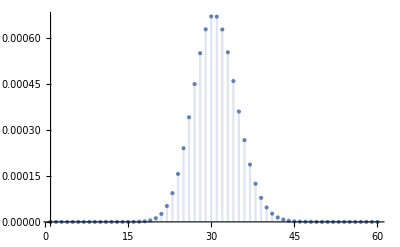

```mathematica
DiscretePlot[p[k,2]/.{λ1->12, λ2->20},{k,1,60}]
```

4. Zgłoszenia napływają do serwera zgodnie z procesem Poissona z parametrem λ.
(a) Dla wartości λ = 2, 4, 6, 8 [/min] oblicz i przedstaw w tabeli i w formie graficznej prawdopodobieństwo, że w ciągu dwóch minut pojawi się k (=0,...,10) zgłoszeń.
(b) Dla wartości λ z (a) i t=0.1, 0.2, ..., 1 przedstaw w tabeli i w formie graficznej prawdopodobieństwa, że odstęp pomiędzy kolejnymi zgłoszeniami będzie mniejsza niż t
(c) Dla tych samych λ przedstaw w formie graficznej rozkład czasu do pojawienia się 5, 10, 15, i 20 zgłoszeń.

a)

```mathematica
praw = Table[P = PoissonProcess[i];
a =Probability[m[2]==j,m\[Distributed]P],{i,2,8,2},{j,0,10}];
```

```mathematica
Grid[praw,Frame->All];
```

```mathematica
%39
```

1/ⅇ^4 | 4/ⅇ^4 | 8/ⅇ^4 | 32/(3 ⅇ^4) | 32/(3 ⅇ^4) | 128/(15 ⅇ^4) | 256/(45 ⅇ^4) | 1024/(315 ⅇ^4) | 512/(315 ⅇ^4) | 2048/(2835 ⅇ^4) | 4096/(14175 ⅇ^4)
1/ⅇ^8 | 8/ⅇ^8 | 32/ⅇ^8 | 256/(3 ⅇ^8) | 512/(3 ⅇ^8) | 4096/(15 ⅇ^8) | 16384/(45 ⅇ^8) | 131072/(315 ⅇ^8) | 131072/(315 ⅇ^8) | 1048576/(2835 ⅇ^8) | 4194304/(14175 ⅇ^8)
1/ⅇ^12 | 12/ⅇ^12 | 72/ⅇ^12 | 288/ⅇ^12 | 864/ⅇ^12 | 10368/(5 ⅇ^12) | 20736/(5 ⅇ^12) | 248832/(35 ⅇ^12) | 373248/(35 ⅇ^12) | 497664/(35 ⅇ^12) | 2985984/(175 ⅇ^12)
1/ⅇ^16 | 16/ⅇ^16 | 128/ⅇ^16 | 2048/(3 ⅇ^16) | 8192/(3 ⅇ^16) | 131072/(15 ⅇ^16) | 1048576/(45 ⅇ^16) | 16777216/(315 ⅇ^16) | 33554432/(315 ⅇ^16) | 536870912/(2835 ⅇ^16) | 4294967296/(14175 ⅇ^16)

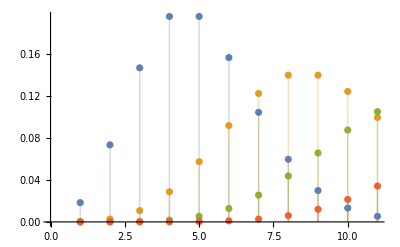

```mathematica
ListPlot[Table[P = PoissonProcess[i];
a =Probability[m[2]==j,m\[Distributed]P],{i,2,8,2},{j,0,10}],Filling->Axis]
```

b)

```mathematica
s = Table[P=PoissonProcess[i];
a =Probability[m[y]<t,m\[Distributed]P],{i,2,8,2},{t,0.1,1, 0.1}];
Grid[s,Frame->All]
```

ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y) | ⅇ^(-2 y)
ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y) | ⅇ^(-4 y)
ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y) | ⅇ^(-6 y)
ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y) | ⅇ^(-8 y)

c)

```mathematica
s = Table[P=PoissonProcess[i];
a =Probability[m[y]==j,m\[Distributed]P],{i,2,8,2},{j,5,20, 5}];
Grid[s,Frame->All]
```

4/15 ⅇ^(-2 y) y^5 | (4 ⅇ^(-2 y) y^10)/14175 | (16 ⅇ^(-2 y) y^15)/638512875 | (4 ⅇ^(-2 y) y^20)/9280784638125
128/15 ⅇ^(-4 y) y^5 | (4096 ⅇ^(-4 y) y^10)/14175 | (524288 ⅇ^(-4 y) y^15)/638512875 | (4194304 ⅇ^(-4 y) y^20)/9280784638125
324/5 ⅇ^(-6 y) y^5 | 2916/175 ⅇ^(-6 y) y^10 | (314928 ⅇ^(-6 y) y^15)/875875 | (2125764 ⅇ^(-6 y) y^20)/1414538125
4096/15 ⅇ^(-8 y) y^5 | (4194304 ⅇ^(-8 y) y^10)/14175 | (17179869184 ⅇ^(-8 y) y^15)/638512875 | (4398046511104 ⅇ^(-8 y) y^20)/9280784638125